```mathematica
Remove["Global`*"]
```

```mathematica
FourierTransform[Sin[W*x],x,k]
```

ⅈ √(π/2) DiracDelta[k-W]-ⅈ √(π/2) DiracDelta[k+W]

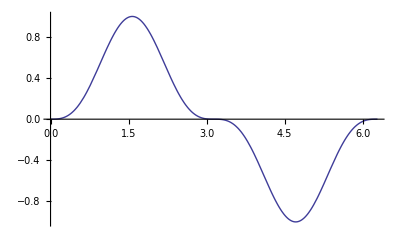

```mathematica
Plot[Sin[x]^3,{x,0,2*Pi}]
```

```mathematica
FourierTransform[Sin[W*x]^3,x,k]
```

-1/4 ⅈ √(π/2) DiracDelta[k-3 W]+3/4 ⅈ √(π/2) DiracDelta[k-W]-3/4 ⅈ √(π/2) DiracDelta[k+W]+1/4 ⅈ √(π/2) DiracDelta[k+3 W]

```mathematica
ft[k_] = FourierTransform[1/(1+x^2),x,k]
```

ⅇ^(-Abs[k]) √(π/2)

```mathematica
InverseFourierTransform[ft[k],k,x]
```

1/(1+x^2)

```mathematica
Clear[f]
```

```mathematica
FourierTransform[f'[x],x,k]
```

-ⅈ k FourierTransform[f[x],x,k]

```mathematica
FourierTransform[Exp[I*A*x],x,k]
```

√(2 π) DiracDelta[A+k]

```mathematica
FourierTransform[Exp[I*A*x],x,k,FourierParameters->{-1,1}]
```

DiracDelta[A+k]

```mathematica
FourierTransform[Cos[A*x],x,k,FourierParameters->{-1,1}]
```

1/2 DiracDelta[-A+k]+1/2 DiracDelta[A+k]

```mathematica
FourierTransform[DiracDelta[x-A],x,k]
```

(Cos[A k]+ⅈ Sin[A k])/(√(2 π))

```mathematica
FourierTransform[Sign[x],x,k]
```

(ⅈ √(2/π))/k

```mathematica
D[Sign[x],x]
D[UnitStep[x],x]
```

Sign'[x]

Piecewise[{{Indeterminate, x==0}, {0, True}}]

```mathematica
FourierTransform[UnitStep[x],x,k]
```

ⅈ/(k √(2 π))+√(π/2) DiracDelta[k]

```mathematica
FourierTransform[Exp[-a*x]*UnitStep[x],x,k]
```

1/((a-ⅈ k) √(2 π))

```mathematica
FourierTransform[x*Exp[-a*x]*UnitStep[x],x,k]
```

1/((a-ⅈ k)^2 √(2 π))

```mathematica
FourierTransform[Exp[-A*x^2],x,k]
```

(ⅇ^(-k^2/(4 A)))/(√2 √A)

```mathematica
Hat[x_] := P*(UnitStep[Q+x]+UnitStep[Q-x]-1)
```

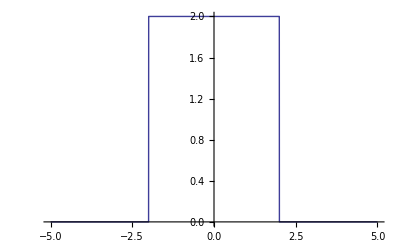

```mathematica
Plot[Hat[x]/.{P->2,Q->2},{x,-5,5}]
```

```mathematica
FourierTransform[Hat[x],x,k]
```

(P √(2/π) Sin[k Q])/k

```mathematica
Phat[k_,Q_]=FourierTransform[Hat[x]/.P->1,x,k]
```

(√(2/π) Sin[k Q])/k

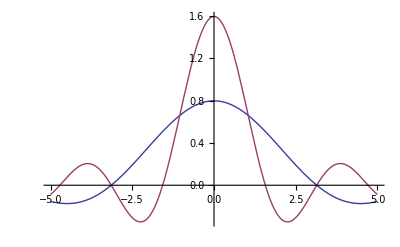

```mathematica
Plot[{Phat[k,1],Phat[k,2]},{k,-5,5}]
```

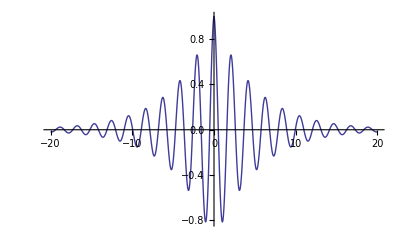

```mathematica
Plot[Exp[-0.2*Abs[x]]*Cos[3*x],{x,-20,20},PlotRange->All]
```

```mathematica
FourierTransform[Exp[-A*Abs[x]]*Cos[B*x],x,k]
```

A/((A^2+B^2-2 B k+k^2) √(2 π))+A/((A^2+(B+k)^2) √(2 π))

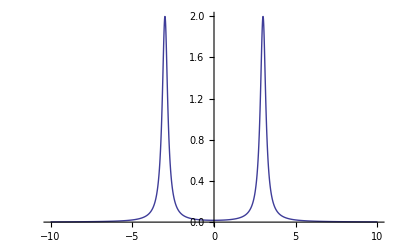

```mathematica
Plot[A/((A^2+B^2-2 B k+k^2) √(2 π))+A/((A^2+(B+k)^2) √(2 π))/.{A->0.2,B->3},{k,-10,10},PlotRange->All]
```

```mathematica
FourierTransform[Sin[x],x,k]
```

ⅈ √(π/2) DiracDelta[-1+k]-ⅈ √(π/2) DiracDelta[1+k]

```mathematica
LaplaceTransform[Sin[x],x,k]
```

1/(1+k^2)

```mathematica
x[s_]:=0;
t[s_]:=s;
FourierTransform[Exp[-I*Ω*(t[s]-x[s]/c)],s,ω]
```

√(2 π) DiracDelta[ω-Ω]

```mathematica
x[s_]:=V;
t[s_]:=V*s;
FourierTransform[Exp[-I*Ω*(t[s]-x[s]/c)],s,ω]
```

ⅇ^((ⅈ V Ω)/c) √(2 π) DiracDelta[ω-V Ω]

```mathematica
FullSimplify[Solve[ω-Ω+V*Ω/c==0,ω]]
```

{{ω→Ω-(V Ω)/c}}

```mathematica
x[s_]:=Vs;
t[s_]:=V*s;
FourierTransform[Exp[-I*Ω*(t[s]-x[s]/c)],s,ω]
```